```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", FileNameJoin[{NotebookDirectory[],"NoisyQuantumTeleportationBenchmarking.wl"}]]
```

```mathematica
teoricos = Import["teorico.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
Importar[fileName_] := Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"qpu-results", fileName}], "Dataset", "HeaderLines"->1]
```

```mathematica
(*ResourceFunction["MaTeXInstall"][];
<<MaTeX`*)
```

```mathematica
backends = {"ibm_brisbane", "ibm_sherbrooke"};(*, "ibm_kyiv"*)
plotMarker["ibm_brisbane"] := "☐";
plotMarker["ibm_sherbrooke"] := "⦿";
```

```mathematica
latexStyle = {FontFamily ->  "LM Roman 12"};
colores = ColorData[97,"ColorList"];
axesLabels = {MaTeX["p"], MaTeX["\langle \\bar{F} \\rangle"]};
```

```mathematica
ps = {0, 0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8, 0.9, 1};puntosParaDataset[ds_] := Table[{p, ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==p && #pB ==p)&], "score"][1]}, {p, ps}];
puntosParaDatasetFNWN[ds_] := Table[{p, ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==0.85 && #pB ==p)&], "score"][1]}, {p, ps}];
```

```mathematica
experimentosDiagonal={"diagonal_unoptimized", "diagonal_QPU_optimized", "diagonal_QPU_optimized_EM"};
```

```mathematica
GraficarParaBackend[backend_] := ListLinePlot[{puntosParaDataset[teoricos]}~Join~((e|->puntosParaDataset[Importar[backend<>"_"<>e<>".csv"]])/@ experimentosDiagonal), BaseStyle -> latexStyle,Joined->True, PlotStyle->colores, PlotMarkers->{""}~Join~ConstantArray[plotMarker[backend],Length[experimentosDiagonal]] , AxesLabel->axesLabels];
```

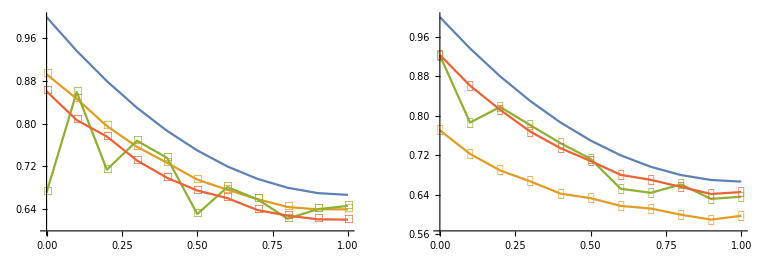

```mathematica
Legended[GraphicsRow[GraficarParaBackend /@ backends],LineLegend[colores, (Text[#, BaseStyle->latexStyle]&)/@({"teóricos"}~Join~experimentosDiagonal)]]
```

```mathematica
res = {0.6540994448735805,0.6591411538058255,0.6638033871712585,0.6680123449734643,0.6716666666666666,0.6746204262508609,0.6766496580927726,0.6773773447853213,0.6760683602522959,0.6708248290463863,0.6416666666666666};
```

```mathematica
teo = Table[{(i-1)/10, res[[i]]}, {i,11}];
plot = ListLinePlot[{Labeled[teo, "teóricos"]}~Join~((b |->Labeled[puntosParaDatasetFNWN[Importar[b<>"_fighting_noise_with_noise.csv"]], b])/@ backends), BaseStyle -> latexStyle, Joined->True, PlotMarkers->{""}~Join~(plotMarker /@ backends), PlotStyle->{colores[[1]]}~Join~ConstantArray[colores[[4]],Length[backends]] , AxesLabel->axesLabels];
line=Plot[Labeled[2/3, MaTeX["\langle \\bar{F} \\rangle_{cl}"]],{x,0,1}];Show[plot,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```

-Graphics-